```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

## T-Filling

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata\NStar

Runs in the list: {12666,12667,12668,12669}

Size: 4

-1.74595+1.11186 x-0.0188532 x^2

7.8924+1.09234 x-0.0186171 x^2

{14.6471,{x→29.4875}}

{23.9154,{x→29.337}}

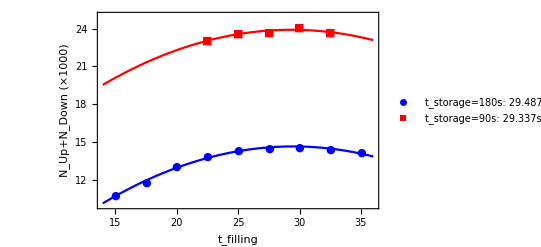

Number of Cycles: 9.

```mathematica
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata\\NStar"];
];
Print["Runs in the list: ",runNum={12666,12667,12668,12669}];(*11159,11369*)
Print["Size: ",Dimensions[runNum][[1]]];
metadata=Table[{},{k,0,Dimensions[runNum][[1]]}];
For[i=1,i≤Dimensions[runNum][[1]],i++,
metadata[[i]]=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[i]],10,6],"_Meta3.edm"],metaStructure2];
];
dat=Table[{15+((k-1)2.5),{(metadata[[1]][[k]][[27]]+metadata[[1]][[k]][[28]]+metadata[[2]][[k]][[27]]+metadata[[2]][[k]][[28]])/2000,Sqrt[(metadata[[1]][[k]][[27]]+metadata[[1]][[k]][[28]]+metadata[[2]][[k]][[27]]+metadata[[2]][[k]][[28]])/2]/1000}},{k,1,9}];
dat2=Table[{22.5+((k-1)2.5),{(metadata[[3]][[k]][[27]]+metadata[[3]][[k]][[28]]+metadata[[4]][[k]][[27]]+metadata[[4]][[k]][[28]])/2000,Sqrt[(metadata[[3]][[k]][[27]]+metadata[[3]][[k]][[28]]+metadata[[4]][[k]][[27]]+metadata[[4]][[k]][[28]])/2]/1000}},{k,1,5}];
fit1=Fit[Table[{15+((k-1)2.5),(metadata[[1]][[k]][[27]]+metadata[[1]][[k]][[28]]+metadata[[2]][[k]][[27]]+metadata[[2]][[k]][[28]])/2000},{k,1,9}],{1,x,x^2},x]
fit2=Fit[Table[{22.5+((k-1)2.5),(metadata[[3]][[k]][[27]]+metadata[[3]][[k]][[28]]+metadata[[4]][[k]][[27]]+metadata[[4]][[k]][[28]])/2000},{k,1,5}],{1,x,x^2},x]
FindMaximum[fit1,x]
FindMaximum[fit2,x]
Show[{
EDAListPlot[dat,dat2,PlotLegends->{StringJoin["t_storage=180s: ",ToString[x/.FindMaximum[fit1,x][[2]][[1]]],"s"],StringJoin["t_storage=90s: ",ToString[x/.FindMaximum[fit2,x][[2]][[1]]],"s"]},PlotStyle->{Blue,Red},PlotRange->{{14,36},{10,25}},Frame->True,FrameLabel->{"t_filling","N_Up+N_Down (×1000)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{-1.7459545454545262+1.1118646753246753 x-0.01885316017316018 x^2,7.892399999999783+1.0923428571428726 x-0.018617142857143127 x^2},{x,14,36},PlotStyle->{Blue,Red},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
Print["Number of Cycles: ",maxCy=metadata[[1]][[-1]][[2]]];
```

## T-Monitor

```mathematica
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
Print["Runs in the list: ",runNum={12673}];
Print["#Runs in the list: ",runn=Dimensions[runNum][[1]]];
bkgcou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
moncou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
Monitor[
icycle=0;
histbeg2=0*(10^9);histlast2=300*(10^9);binw2=1*(10^9);
For[runi=1,runi≤1(*runn*),runi++,
Clear[data,histdata2];
maxCy=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta3.edm"],metaStructure2][[-1]][[2]];
ptdat2=Table[Table[{0,{0,0}},{k,1,Round[(histlast2-histbeg2)/binw2]}],{l,1,maxCy}];
bkgcou[[runi]]={};
moncou[[runi]]={};
For[icycle=1,icycle≤ maxCy,icycle++,
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Read Cycle #",icycle];
dimdata=Dimensions[data][[1]];
histdata2=HistogramList[data[[1;;dimdata,4]],{histbeg2,histlast2,binw2}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[icycle]][[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2))/(10^9);
ptdat2[[icycle]][[i]][[2]][[1]]=histdata2[[2]][[i]];
ptdat2[[icycle]][[i]][[2]][[2]]=Sqrt[ptdat2[[icycle]][[i]][[2]][[1]]];
bkgcou[[runi]]=
AppendTo[bkgcou[[runi]],Abs[Total[ptdat2[[icycle]][[;;,2]][[;;,1]][[218-66;;218]]]-Floor[Mean[ptdat2[[icycle]][[;;,2]][[;;,1]][[218-99;;218]]]*67]]];
moncou[[runi]]=
AppendTo[moncou[[runi]],N[Mean[ptdat2[[icycle]][[;;,2]][[;;,1]][[218-99;;218]]]]];
];
];
];,
ProgressIndicator[icycle/maxCy,ImageSize->{1000,100}]]
ProgressIndicator[1,ImageSize->{1000,100}]
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {12673}

#Runs in the list: 1

Read Cycle #1

Read Cycle #2

Read Cycle #3

Read Cycle #4

Read Cycle #5

Read Cycle #6

Read Cycle #7

Read Cycle #8

Read Cycle #9

Read Cycle #10

```mathematica
Clear[nlm,aa]
pt=Table[0,{k,1,maxCy}];
For[icycle=1,icycle≤maxCy,icycle++,
Print["Cycle # ",icycle];
ftdat=Table[Transpose[{ptdat2[[icycle]][[;;,1]],ptdat2[[icycle]][[;;,2]][[;;,1]]}][[k]],{k,35,180}];
nlm=NonlinearModelFit[ftdat,{aa+(bb Exp[cc (xx-dd)])},{{aa,1},{bb,30000},{cc,-.4},{dd,33}},xx,Method->NMinimize];
fitparam={aa/.nlm[[1]][[2]],bb/.nlm[[1]][[2]],cc/.nlm[[1]][[2]],dd/.nlm[[1]][[2]]};
fitparamerr=SetPrecision[N[nlm["ParameterErrors"]],10];
pt[[icycle]]=EDALogListPlot[ptdat2[[icycle]]+.1, PlotStyle->{Blue},Joined->True,Filling->Axis,PlotRange->{{0,300},{1,100000}},Frame->True,InterpolationOrder->3,FrameLabel->{"Time (s)","UCN Counts (#)"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,PlotLabel->StringJoin["t_monitor = ",ToString[Round[2*icycle]]," s"],FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}];
];
width=2;
Export["nstar-t_monitor.png",GraphicsGrid[ArrayReshape[pt,{Ceiling[maxCy/width],width}]]]
```

Cycle # 1

Cycle # 2

Cycle # 3

Cycle # 4

Cycle # 5

Cycle # 6

Cycle # 7

Cycle # 8

Cycle # 9

Cycle # 10

nstar-t_monitor.png

```mathematica
Show[{
EDALogListPlot[ptdat2[[icycle]]+.1, PlotStyle->{Blue},Joined->True,Filling->Axis,PlotRange->{{0,300},{1,40000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
EDALogListPlot[Table[{k,Abs[fitparam[[1]]+fitparam[[2]]Exp[fitparam[[3]](k-fitparam[[4]])]]},{k,33,288}], PlotStyle->{Red},Joined->True,Filling->Axis,PlotRange->{{0,300},{.1,40000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}]
}]
```

$Aborted

## T-Emptying

```mathematica
Print["Runs in the list: ",runNum={12674}];
Print["#Runs in the list: ",runn=Dimensions[runNum][[1]]];
bkgcou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
moncou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
Monitor[
icycle=0;
histbeg2=0*(10^9);histlast2=600*(10^9);binw2=1*(10^9);
For[runi=1,runi≤1(*runn*),runi++,
Clear[data,histdata2];
maxCy=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta3.edm"],metaStructure2][[-1]][[2]];
ptdat2=Table[Table[{0,{0,0}},{k,1,Round[(histlast2-histbeg2)/binw2]}],{l,1,maxCy}];
bkgcou[[runi]]={};
moncou[[runi]]={};
For[icycle=1,icycle≤ maxCy,icycle++,
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Read Cycle #",icycle];
dimdata=Dimensions[data][[1]];
histdata2=HistogramList[data[[1;;dimdata,4]],{histbeg2,histlast2,binw2}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[icycle]][[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2))/(10^9);
ptdat2[[icycle]][[i]][[2]][[1]]=histdata2[[2]][[i]];
ptdat2[[icycle]][[i]][[2]][[2]]=Sqrt[ptdat2[[icycle]][[i]][[2]][[1]]];
];
];
];,
ProgressIndicator[icycle/maxCy,ImageSize->{1000,100}]]
ProgressIndicator[1,ImageSize->{1000,100}]
```

Runs in the list: {12674}

#Runs in the list: 1

Read Cycle #1

Read Cycle #2

Read Cycle #3

```mathematica
Clear[nlm,aa]
pt=Table[0,{k,1,maxCy}];
For[icycle=3,icycle≤maxCy,icycle++,
Print["Cycle # ",icycle];
ftdat=Table[Transpose[{ptdat2[[icycle]][[;;,1]],ptdat2[[icycle]][[;;,2]][[;;,1]]}][[k]],{k,Round[(icycle-1)*180+55],Round[(icycle-1)*180+110]}];
nlm=NonlinearModelFit[ftdat,{aa+(bb Exp[cc (xx-dd)])},{{aa,1},{bb,30000},{cc,-.4},{dd,33}},xx,Method->NMinimize];
fitparam={aa/.nlm[[1]][[2]],bb/.nlm[[1]][[2]],cc/.nlm[[1]][[2]],dd/.nlm[[1]][[2]]};
fitparamerr=SetPrecision[N[nlm["ParameterErrors"]],10];
pt[[icycle]]=Show[{
EDALogListPlot[ptdat2[[icycle]]+.1, PlotStyle->{Blue},Joined->True,Filling->Axis,PlotRange->{{0,600},{1,40000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium},
PlotLabel->StringJoin["t_s = ",ToString[Round[((icycle-1)*180)+10]]," s, N_EmptyingExp[",ToString[fitparam[[3]]],"(t-t_0)]"]],
EDALogListPlot[Table[{k,Abs[fitparam[[1]]+fitparam[[2]]Exp[fitparam[[3]](k-fitparam[[4]])]]},{k,Round[(icycle-1)*180+55],Round[(icycle-1)*180+110]}], PlotStyle->{Red},Joined->True,Filling->Axis,PlotRange->{{0,600},{.1,40000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, None}]
}];
];
width=3;
Export["t_emptying.png",GraphicsGrid[ArrayReshape[pt,{Ceiling[maxCy/width],width}]]]
```

Cycle # 3

t_emptying.png

```mathematica
fitparam
```

{-0.423343,233030.,-0.0835805,340.148}

75

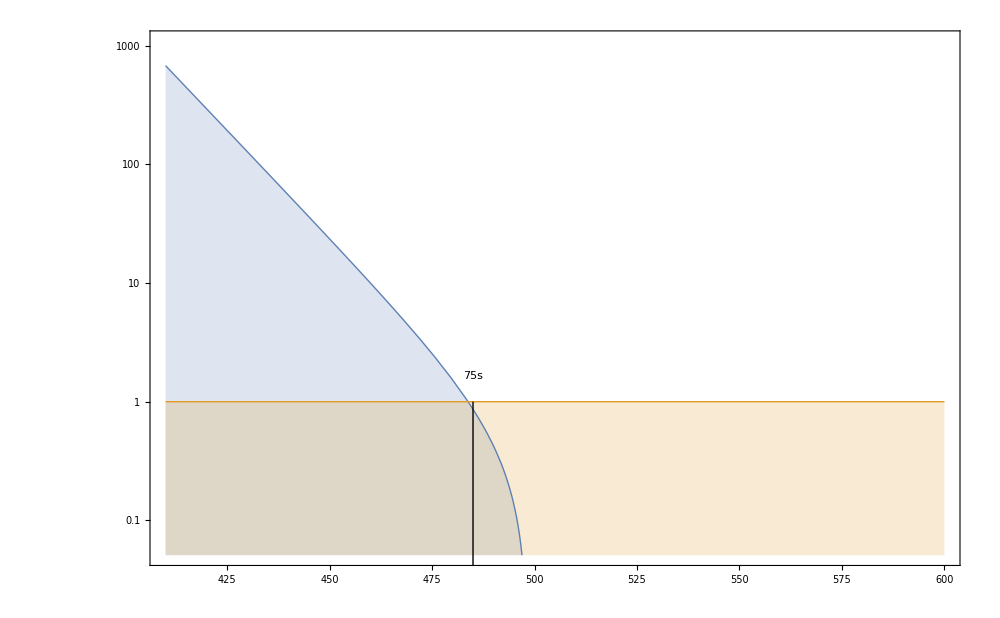

```mathematica
func3[xx_]:=fitparam[[1]]+(fitparam[[2]] Exp[fitparam[[3]] (xx-fitparam[[4]])])
st=410;
diff=75
end=st+diff;
LogPlot[{func3[xx],1},{xx,410,600},PlotRange->{{410,600},{0,1100}},Filling->Axis,PlotStyle->Thick,Frame->True,ImageSize->1000,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,Epilog->{Line[{{end,-1000},{end,0}}],Text[Style[StringJoin[ToString[diff],"s"],FontSize->Large],{end,0.5}]}]
lineStyle={Thin,Gray,Dashed};
line11=Line[{{0,6000},{16,6000}}];
```

```mathematica
(3-1)*180+55
```

415